Auxiliary notebook to get the coordinates of the patchy particles.
Also analyse the potentials and energy wells.

#### Coordinates of the Patchy particles

a is the length of the tetrahedron.

```mathematica
Vertex = Function[a,a {{0,0,√(2/3)-1/(2 √6)},{-1/(2 √3),-1/2,-1/(2 √6)},{-1/(2 √3),1/2,-1/(2 √6)},{1/(√3),0,-1/(2 √6)}}]
```

Function[a,a {{0,0,√(2/3)-1/(2 √6)},{-1/(2 √3),-1/2,-1/(2 √6)},{-1/(2 √3),1/2,-1/(2 √6)},{1/(√3),0,-1/(2 √6)}}]

```mathematica
centers = Vertex[3/4]
N[centers,2]
Graphics3D[
	Append[
		Table[Sphere[centers[[i]],0.25],{i,Length[centers]}],
		{Opacity[0.5],Sphere[{0,0,0},0.5]}
		]
	]
```

{{0,0,3/4 (√(2/3)-1/(2 √6))},{-(√3)/8,-3/8,-(√(3/2))/8},{-(√3)/8,3/8,-(√(3/2))/8},{(√3)/4,0,-(√(3/2))/8}}

{{0,0,0.46},{-0.22,-0.38,-0.15},{-0.22,0.38,-0.15},{0.43,0,-0.15}}

-Graphics3D-

#### Stuff of the potentials

σ is the radius of the particle in Ovito :)
σ is the distance between the center of the particles in LAMMPS

```mathematica
σCL = 1;
σMO = 1;
σPA = 0.5;
σPB = 0.5;
rcCL = 2^(1/6)σCL
rcMO = 2^(1/6)σMO
rcPA = 2^(1/6)σPA
rcPB = 2^(1/6)σPB
```

2^(1/6)

2^(1/6)

0.561231

0.561231

```mathematica
rcCL//N
```

1.12246

```mathematica
LJP[ϵ_,σ_,r_]:= 4 ϵ((σ/r)^12 - (σ/r)^6)
SWP[ϵ_,σ_,A_,B_,a_,p_,q_,r_]:= A ϵ (B (σ/r)^p - (σ/r)^q)Exp[σ/(r-a σ)]
ISP[ϵ_,σ_,rc_,r_]:= 2 ϵ ((σ/r)^4 - 1)Exp[σ/(r-rc)+2]
```

```mathematica
SWP[ϵ,σ,A,B,a,p,q,r]
SWP[ϵ,σ,2,1,1.5,p,0,r]
```

A ⅇ^(σ/(r-a σ)) ϵ (B (σ/r)^p-(σ/r)^q)

2 ⅇ^(σ/(r-1.5 σ)) ϵ (-1+(σ/r)^p)

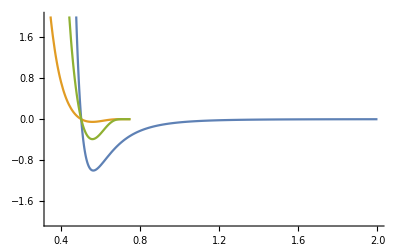

```mathematica
Module[{epLJ=1,sigLJ=0.5,epSW=1,sigSW=0.5,ASW=2,BSW=1,aSW=1.5,pSW=4,qSW=0,rm=2},
	Plot[{
		LJP[epLJ,sigLJ,s],
		SWP[epSW,sigSW,ASW,BSW,aSW,pSW,qSW,s],
		ISP[epSW,sigSW,1.5 sigSW,s]
	},{s,0,rm},
	PlotRange->{All,{-2 epLJ, 2 epLJ}}
	]
]
```

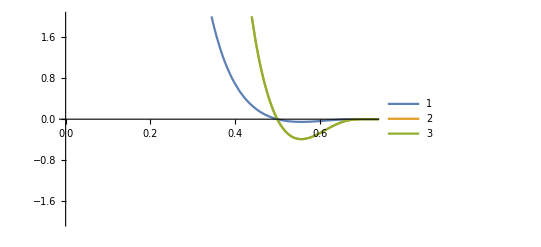

```mathematica
Module[{epLJ=1,sigLJ=0.5,epSW=1,sigSW=0.5,ASW=2,BSW=1,aSW=1.5,pSW=4,qSW=0,rm=2},
	Plot[{
		SWP[epSW,sigSW,ASW,BSW,aSW,pSW,qSW,s],
		ISP[epSW,sigSW,1.5 sigSW,s],
		SWP[7.38905609893065 epSW,sigSW,ASW,BSW,aSW,pSW,qSW,s]
	},{s,0,rm},
	PlotRange->{{0,0.725},{-2 epLJ, 2 epLJ}},
	PlotLegends->Automatic
	]
]
```

```mathematica
SWP[ϵs,σ,2,1,1.5,4,0,r]
ISP[ϵp,σ,1.5 σ,r]

Solve[Simplify[SWP[ϵs,σ,2,1,1.5,4,0,r]==ISP[ϵp,σ,1.5 σ,r]],ϵs]
```

2 ⅇ^(σ/(r-1.5 σ)) ϵs (-1+σ^4/r^4)

2 ⅇ^(2+σ/(r-1.5 σ)) ϵp (-1+σ^4/r^4)

{{ϵs→7.38906 ϵp}}

```mathematica
0.25*1.5
```

0.375

```mathematica
0.5*1.25
```

0.625